```mathematica
ClearAll;
```

```mathematica
kEC = 1.60217733 10^-19;
kAMC = 1.660538921 10^-27;
kC=N[(2 kEC)/kAMC]
```

1.92971×10^8

```mathematica
A[m_,V_,L_]:=(V kEC)/(m kAMC L)
```

```mathematica
acceleratorVoltage[ t_, length_, m_ ] := length^2 m / (t^2 kC);
```

```mathematica
d = { 0.06626, 0.30512, 0.66273,  0.0 };
L[n_] := d[[3]]  n               (* Compute length (m) at n-laps *)
fLength[n_]:=d[[1]] + d[[1]] + d[[2]] + d[[4]] + n  d[[3]]  (*length with injection+ejection*)
sLength[n_] := d[[1]] + d[[1]] + d[[2]] + n  d[[3]]
```

```mathematica
T[m_,V_,L_]:=(L √m)/(√V √kC);
```

```mathematica
t2m[t_,V_,l_]:=(kC t^2 V)/l^2
```

```mathematica
mAr = 39.96183454;
mMe = 16.03075155;
mN2 = 28.00559943;
mXe = 131.9036049;
```

```mathematica
Me = {{6.3371784 10^-05,20},{9.9921119 10^-05,32},{1.5474489 10^-04,50}};
N2 ={{8.3684315 10^-05,20},{1.2393971 10^-04,30}};
Ar = { {9.9916768 10^-5, 20},{1.4800454 10^-4,  30 }};
Xe = { {1.8133327 10^-04, 20},{2.6869789 10^-04, 30},{4.4342763 10^-04, 50}  };
M = { Me,N2,Ar,Xe};
masses = {mMe, mN2,mAr,mXe};
```

```mathematica
(*mm[[mass]][[ [tof,lap],[tof,lap] ]]*)
MM = {{ mMe,{{6.3371784 10^-05,20},{9.9921119 10^-05,32}}}
,{mMe, {{9.9921119 10^-05,32},{1.5474489 10^-04,50}}}
,{mN2,{{8.3684315 10^-05,20},{1.2393971 10^-04,30}}}
,{mAr,{{9.9916768 10^-5, 20},{1.4800454 10^-4,  30 }}}
,{mXe,{{1.8133327 10^-04, 20},{2.6869789 10^-04, 30}}}
,{mXe,{{2.6869789 10^-04, 30},{4.4342763 10^-04, 50}}}
};
MTOF = {{ mMe,{6.3371784 10^-05,20}}
,{mMe, {9.9921119 10^-5,32}}
,{mMe,{1.5474489 10^-4,50}}
,{mN2,{8.3684315 10^-5,20}}
,{mN2,{1.2393971 10^-4,30}}
,{mAr,{9.9916768 10^-5, 20}}
,{mAr,{1.4800454 10^-4,  30 }}
,{mXe,{1.8133327 10^-4, 20}}
,{mXe,{2.6869789 10^-4, 30}}
,{mXe,{4.4342763 10^-4, 50}}
};
```

```mathematica
fVelocity[dlap_] := d[[3]]/(dlap[[1]]/dlap[[2]])
tlap[mat_] := mat[[1]]/mat[[2]];                                       (*lap-time*)
tHalfCycle[a_,b_] := b[[1]]-tlap[b-a]*b[[2]]  (* flight-time for half-cycle part *)
lHalfCycle[mm_]         := tHalfCycle[mm[[2,2]],mm[[2,1]]] * fVelocity[mm[[2,2]]-mm[[2,1]]];
halfCycleTime[mm_] := mm[[2,2]][[1]]-tlap[mm[[2,2]]-mm[[2,1]]]*mm[[2,2]][[2]];
```

#### Accelerator voltage estimation

```mathematica
(*hfunctor[mm_] := tHalfCycle @@ mm;; hfunctor /@ MM[[All,2]] *)
hcTimes = tHalfCycle @@ #& /@ MM[[All,2]] (* time for half-cycle mode *)
hcLength = lHalfCycle /@ MM
hcVa = acceleratorVoltage @@ #& /@ Transpose[{hcTimes,hcLength,MM[[All,1]]}]
```

{2.45623×10^-6,2.45664×10^-6,3.17353×10^-6,3.74122×10^-6,6.60403×10^-6,6.60328×10^-6}

{0.534449,0.534541,0.522462,0.515603,0.500968,0.50091}

{3933.14,3933.17,3933.49,3933.31,3933.39,3933.37}

FittedModel[3933.17+0.0203926 x]

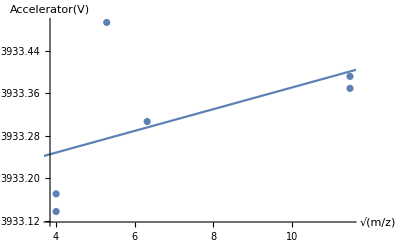

```mathematica
hcdata = Transpose[{Sqrt[MM[[All,1]]],hcVa}];
hcm= LinearModelFit[ hcdata, x,x]
Show[ ListPlot[ hcdata, AxesLabel->{Sqrt[m/z],"Accelerator(V)"}]
, Plot[hcm[x],{x,1,12} ] ]
```

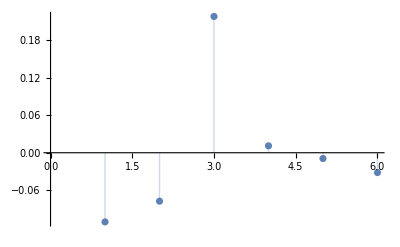

```mathematica
ListPlot[hcm["FitResiduals"], Filling -> Axis]
```

### TOF Equation (scan law) on orbital period

```mathematica
dMM = MM[[All,2,2]]-MM[[All,2,1]]
```

{{0.0000365493,12},{0.0000548238,18},{0.0000402554,10},{0.0000480878,10},{0.0000873646,10},{0.00017473,20}}

{{31.8416,0.0000365493},{47.7624,0.0000548238},{35.0719,0.0000402554},{41.8947,0.0000480878},{76.1141,0.0000873646},{152.228,0.00017473}}

FittedModel[6.32768×10^-10+1.14781×10^-6 x]

{6.32768×10^-10,1.14781×10^-6}

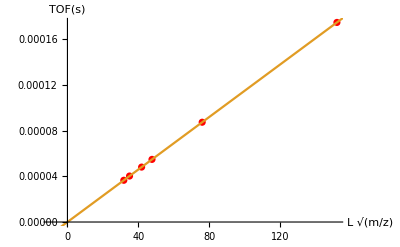

```mathematica
tlaps = Transpose[{ Sqrt[MM[[All,1]]] * L[dMM[[All,2]]],dMM[[All,1]] }]
m0 = LinearModelFit[tlaps, x, x]
{offset0,slope0}=CoefficientList[ Normal[m0],x]
Show[ListPlot[tlaps, PlotStyle -> Red,PlotRange->{{-10,All},Full}]
      ,Plot[{line, m0[x]},{x,-100,400}]
      ,AxesLabel->{L Sqrt[m/z],"TOF(s)"}]
```

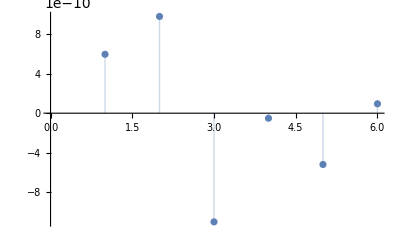

```mathematica
ListPlot[m0["FitResiduals"], Filling -> Axis]
```

```mathematica
Va = acceleratorVoltage[slope0 ,1,1] (* mass = 1, length = 1m*)
```

3933.4

```mathematica
fx[x_] :=offset0 + slope0 * x
m0[(Sqrt[MM[[1,1]]] * L[ dMM[[1,2]] ])]-fx[Sqrt[mMe] * L[12]]; (*validation*)
```

```mathematica
Clear[x,t];
Solve[offs + slope x == t, x];
invfx[t_] := (-offset0 + t)/slope0
```

```mathematica
invfx[dMM[[All,1]]]/Sqrt[MM[[All,1]]]/L[1] (*validation; time -> lap number *)
```

{12.0002,18.0003,9.99973,9.99999,9.99994,20.}

### Compensation length calculation

{{4.00384,4.38369×10^-7},{4.00384,4.34565×10^-7},{4.00384,4.28628×10^-7},{5.29203,5.05593×10^-7},{5.29203,5.00933×10^-7},{6.32154,5.58241×10^-7},{6.32154,5.54629×10^-7},{11.4849,8.26396×10^-7},{11.4849,8.22317×10^-7},{11.4849,8.14658×10^-7}}

FittedModel[2.28581×10^-7+5.16335×10^-8 x]

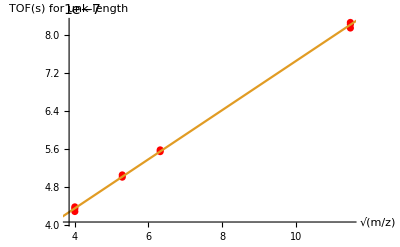

{2.28581×10^-7,5.16335×10^-8}

0.044959528

```mathematica
{tof,lap} = {MTOF[[All,2,1]],MTOF[[All,2,2]]};
uTOF = Transpose[{Sqrt[MTOF[[All, 1]]],(tof  - (fx[Sqrt[MTOF[[All, 1]]]])*sLength[lap] )}]
pu = LinearModelFit[uTOF, x,x]
Show[ListPlot[uTOF, PlotStyle -> Red, PlotRange -> {All, All}]
       , Plot[{line, pu[x]}, {x, 0, 12}], AxesLabel -> {Sqrt[m/z], "TOF(s) for unk-length"}]
uEq = CoefficientList[Normal[pu], x]
d[[4]]  =uEq[[2]]/fx[1];
NumberForm[d[[4]],8]
```

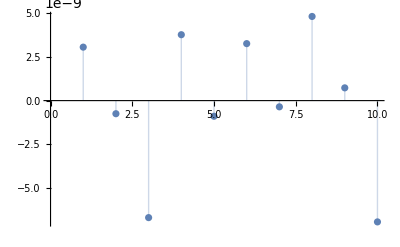

```mathematica
ListPlot[pu["FitResiduals"], Filling -> Axis]
```

### Estimate local (constant accelerated part of) scan-law

```mathematica
{mass,tof,lap}={MTOF[[All,1]],MTOF[[All,2,1]],MTOF[[All,2,2]]};
```

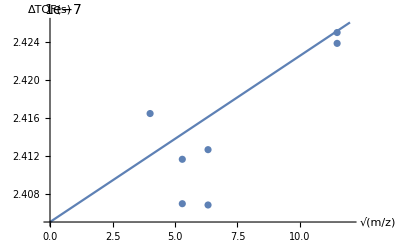

```mathematica
dTof = Transpose[{Sqrt[mass],tof-T[mass,Va,fLength[lap]]}]; (* estimated half cycle flight: Va := Accel(V) from orbital period *)
dTofModel = LinearModelFit[ dTof, x, x];
Show[
Plot[dTofModel[x],{x,0,12}], ListPlot[ dTof], AxesLabel->{Sqrt[m/z],"ΔTOF(s)"}
]
```

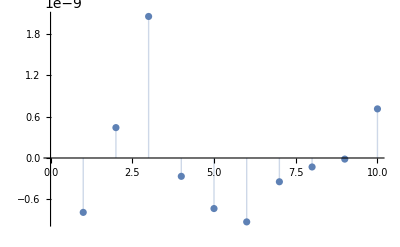

```mathematica
ListPlot[dTofModel["FitResiduals"], Filling -> Axis]
```

```mathematica
Solve[(-v+√(2 a L+v^2))/a==t,a]
```

{{a→-(2 (-L+t v))/t^2}}

```mathematica
fx[intTOF[[All,1]]]
```

{4.59628×10^-6,4.59628×10^-6,4.59628×10^-6,6.07488×10^-6,6.07488×10^-6,7.25656×10^-6,7.25656×10^-6,0.0000131832,0.0000131832,0.0000131832}

```mathematica
fAccel[t_,v_,L_] := (2 (-L+t v) )/t^2
```

```mathematica
fAccel @@ #& /@ Transpose[{intTOF[[All,2]],fx[intTOF[[All,1]]],ConstantArray[0.004,Length[intTOF]]}]
```

{-1.20032×10^11,-1.18898×10^11,-1.17434×10^11,-1.14069×10^11,-1.14472×10^11,-1.10497×10^11,-1.10021×10^11,-9.22538×10^10,-9.21825×10^10,-9.17286×10^10}

### Estimate scan-law (the method where the QtPlatz used)

See infitof/src/libs/infwidgets/mspeakwidget.cpp, estimateScanLaw method

```mathematica
Clear[tof,mass,qt];
{tof,nlap,mass} = { MTOF[[All,2,1]],MTOF[[All,2,2]],MTOF[[All,1]]};
qt=Transpose[{Sqrt[mass] *fLength[nlap],tof}];
```

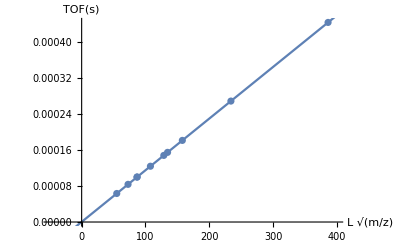

2.40582×10^-7

3933.35

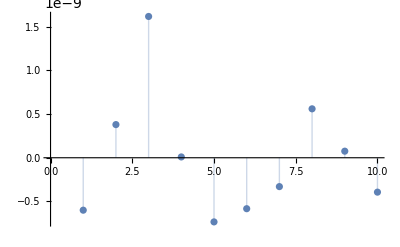

```mathematica
m1 =LinearModelFit[qt,x,x];
Show [ ListPlot[qt,PlotRange->{{-50,400},Full},AxesLabel->{L Sqrt[m/z],"TOF(s)"}]
, Plot[m1[x],{x,-50,400}]]
t0 = m1[0] 
Vacc = acceleratorVoltage[m1[1]-m1[0],1,1] (* mass = 1, length = 1m*)
ListPlot[m1["FitResiduals"], Filling -> Axis]
```

#### // End Scan law Estimation

### Mass errors

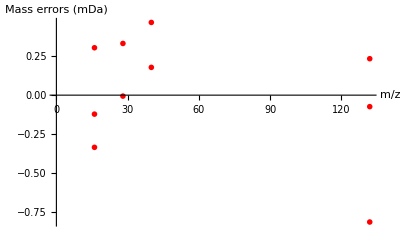

```mathematica
Clear[m,z];
dm = (mass - t2m[tof-t0,Vacc,fLength[nlap]])*1000;
ListPlot[Transpose[{mass,dm}],PlotRange->{{0,All},All}
  , PlotMarkers->"OpenMarkers" ,PlotStyle->Red
, Filling->Axes
,AxesLabel->{m/z,"Mass errors (mDa)"}]
```

### Estimate scan law (by argon)

```mathematica
tof2 = Ar[[All,1]];
lap2 = Ar[[All,2]];
mass2 = ConstantArray[ mAr, Length[Ar]];
pm2=LinearModelFit[Transpose[{Sqrt[mass2] *fLength[lap2],tof2}],x, x];
{t02,slope2}=CoefficientList[Normal[pm2],x];
Vacc2 = acceleratorVoltage[slope2,1,1] (* mass = 1, length = 1m*)
```

3933.31

#### Mass errors (for argon ion based scan law)

```mathematica
dm2 = mass - t2m[ tof - t02, Vacc2, fLength[lap]];
Transpose[{mass,dm2}]
```

{{16.0308,-0.0000888476},{16.0308,-0.000309218},{16.0308,-0.000396248},{28.0056,-0.000454348},{28.0056,0.00012544},{39.9618,-5.68434×10^-14},{39.9618,2.84217×10^-14},{131.904,-0.00104026},{131.904,0.000224876},{131.904,0.000961155}}

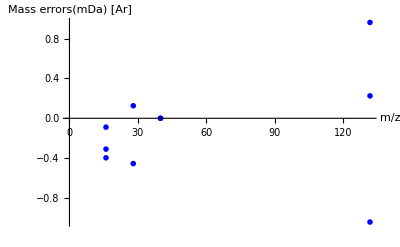

```mathematica
Clear[m,z];
ListPlot[Transpose[{mass,dm2*1000}],PlotRange->{{0,All},All}
,PlotMarkers->"OpenMarkers", PlotStyle->Blue,AxesLabel->{m/z,"Mass errors(mDa) [Ar]"}]
```

### Estimate scan law by using methane ion

```mathematica
{tof3,lap3,mass3} = {Me[[All,1]],Me[[All,2]],ConstantArray[mMe,Length[Me]]};
pm3=LinearModelFit[ Transpose[{Sqrt[mass3] *fLength[lap3],tof3}],x, x];
{t03,slope3}=CoefficientList[Normal[pm3],x];
Vacc3 = acceleratorVoltage[slope3,1,1] (* mass = 1, length = 1m*)
```

3933.16

#### Mass errors (methane)

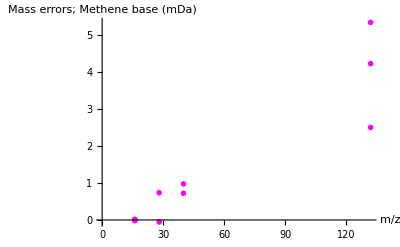

```mathematica
dm3 = (mass - t2m[tof-t03,Vacc3,fLength[lap]])*1000;
ListPlot[Transpose[{mass,dm3}],PlotRange->{{0,All},All}
,PlotMarkers->"OpenMarkers",PlotStyle->Magenta, AxesLabel->{m/z,"Mass errors; Methene base (mDa)"}]
```

### Estimate scan law by using xenon ion

```mathematica
{tof4,lap4,mass4} = {Xe[[All,1]],Xe[[All,2]],ConstantArray[mXe,Length[Xe]]};
pm4=LinearModelFit[ Transpose[{Sqrt[mass4] *fLength[lap4],tof4}],x, x];
{t04,slope4}=CoefficientList[Normal[pm4],x];
Vacc4 = acceleratorVoltage[slope4,1,1] (* mass = 1, length = 1m*)
```

3933.38

#### Mass errors (for xenon ion based scan law)

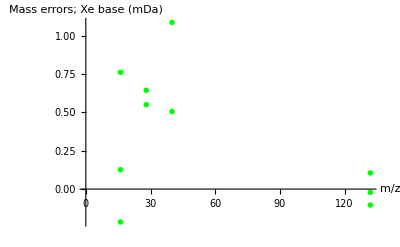

```mathematica
dm4 = (mass - t2m[tof-t04,Vacc4,fLength[lap]])*1000;
ListPlot[Transpose[{mass,dm4}],PlotRange->{{0,All},All}
,PlotMarkers->"OpenMarkers",PlotStyle->Green, AxesLabel->{m/z,"Mass errors; Xe base (mDa)"}]
```

# Constant accelerated equation of motion

```mathematica
S[a_,t_,v_]:=v t+(a t^2)/2
```

```mathematica
Clear[v,t,a,s]
Solve[v t + (a t^2)/2 ==s,t]
```

{{t→(-v-√(2 a s+v^2))/a},{t→(-v+√(2 a s+v^2))/a}}

```mathematica
caTOF[a_,L_,v_]:=(-v+√(2 a L+v^2))/a
fv[a_,t_,v_] := v + a t
```

```mathematica
Show[ Plot[T[m,Va,L]-caTOF[A[m,V,L],L,1/T[m,Va,1]] /.{L->0.004,V->5000},{m,1,200},AxesLabel->{"m/z","Δm"}]
,Plot[T[m,Va,L]-caTOF[A[m,V,L],L,1/T[m,Va,1]] /.{L->0.002,V->5000},{m,1,200},PlotStyle->Red]
,Plot[T[m,Va,L]-caTOF[A[m,V,L],L,1/T[m,Va,1]] /.{L->0.001,V->5000},{m,1,200},PlotStyle->Blue]
,Plot[T[m,Va,L]-caTOF[A[m,V,L],L,1/T[m,Va,1]] /.{L->0.0005,V->5000},{m,1,200},PlotStyle->Green]
];
```

#### TOF (+2nd acceleration)

```mathematica
TOF[m_,n_,Vp_,Vd_,L_] := caTOF[A[Sqrt[m],Vd,L], L, 1/T[m,Vp,1]] + T[m,Vp,fLength[n]-L]
```

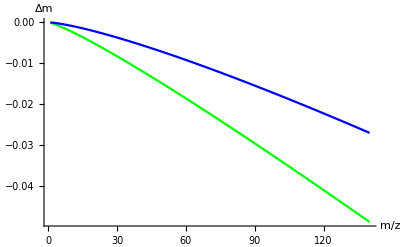

```mathematica
Show[
Plot[ (t2m[TOF[m,n,Vp,Vd,L],Vp,fLength[n]]-m)/.{n->20,Vp->4000,Vd->5000,L->0.004}, {m,1,140},PlotStyle->Green
,AxesLabel->{"m/z","Δm"},PlotRange->{All,All}]
     ,Plot[  (t2m[TOF[m,n,Vp,Vd,L],Vp,fLength[n]]-m)/.{n->20,Vp->4000,Vd->1000,L->0.004}, {m,1,140},PlotStyle->Blue]
]
```

#### Simulated scan law

```mathematica
vTOF = TOF[m,n,Vp,Vd,L]/.{m->132,n->{0,20,40,80,160,1000},Vp->Va,Vd->5000,L->0.004}
```

{6.33276×10^-6,0.000181126,0.000355918,0.000705504,0.00140468,0.00874598}

```mathematica
args = Transpose[{vTOF,fLength[{0,20,40,80,160,1000}],{132,132,132,132,132,132}}];
(*afunctor[av_] := acceleratorVoltage @@av;
afunctor /@ args*)
acceleratorVoltage @@ #&/@args
```

{3972.55,3934.77,3934.1,3933.75,3933.58,3933.43}

```mathematica
afunctor[av_] := acceleratorVoltage @@av;
valist = Transpose[{MTOF[[All,2,2]] (*n-lap*),afunctor /@ Transpose[{MTOF[[All,2,1]]-(t0), fLength[MTOF[[All,2,2]]],MTOF[[All,1]](*Vacc*)}]}]
```

{{20,3933.42},{32,3933.32},{50,3933.27},{20,3933.35},{30,3933.39},{20,3933.39},{30,3933.37},{20,3933.32},{30,3933.35},{50,3933.36}}

```mathematica
(* accelerator(V) from lap *)
dTOF=Transpose[{MM[[All,1]],MM[[All,2,2]]-MM[[All,2,1]]}]; (*lap-tof*)
dargs = Transpose[{dTOF[[All,2,1]],L[dTOF[[All,2,2]]],dTOF[[All,1]]}];
dlist = Transpose[{dTOF[[All,2,2]],afunctor /@ dargs}] (*nlap,Vacc*)
```

{{12,3933.14},{18,3933.17},{10,3933.49},{10,3933.31},{10,3933.39},{20,3933.37}}

```mathematica
vm=LinearModelFit[valist,x,x] (* from observed TOF *)
dm=LinearModelFit[dlist,1, x] (* from orbit TOF *)
```

FittedModel[3933.42-0.00210207 x]

FittedModel[3933.31]

#### Accelerator (V) -- compare value obtained from TOF and theoretical computation.

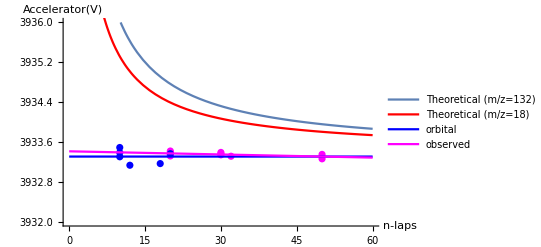

```mathematica
Show[ 
Plot[ acceleratorVoltage[ TOF[m,n,Vp,Vd,L],fLength[n],m]/.{m->132,Vp->Va,Vd->5000,L->0.004}
	,{n,0,60}, PlotRange->{All,{3932,3936}}, AxesLabel->{"n-laps","Accelerator(V)"},PlotLegends->{"Theoretical (m/z=132)"}]
, Plot[ acceleratorVoltage[ TOF[m,n,Vp,Vd,L],fLength[n],m]/.{m->18,Vp->Va,Vd->5000,L->0.004}
	,{n,0,60}, PlotRange->All,PlotStyle->Red,PlotLegends->{"Theoretical (m/z=18)"}]
,ListPlot[valist,PlotRange->All,PlotStyle->Magenta]
, ListPlot[dlist,PlotRange->All,PlotStyle->Blue]
, Plot[dm[n],{n,0,60},PlotStyle->Blue, PlotLegends->{"orbital"}]
,Plot[vm[n],{n,0,60},PlotStyle->Magenta,PlotLegends->{"observed"}]
]
```

#### Effect of MCP IN voltage for mass errors

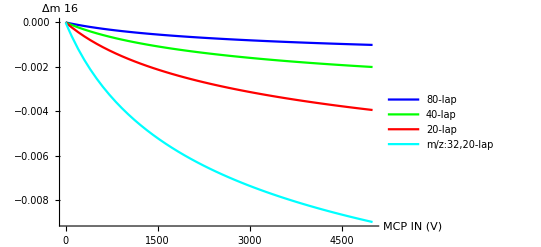

```mathematica
Show[ 
Plot[t2m[ TOF[m,n,Va,V,0.004],Va,fLength[n]]-m/.{m->16,n->80},{V,0,5000}, PlotRange->{All,All},PlotStyle->Blue, AxesLabel->{"MCP IN (V)","Δm 16"},PlotLegends->{"80-lap"}]
, Plot[t2m[ TOF[m,n,Va,V,0.004],Va,fLength[n]]-m/.{m->16,n->40},{V,0,5000},PlotStyle->Green,PlotLegends->{"40-lap"}]
, Plot[t2m[ TOF[m,n,Va,V,0.004],Va,fLength[n]]-m/.{m->16,n->20},{V,0,5000} ,PlotStyle->Red,PlotLegends->{"20-lap"}]
, Plot[t2m[ TOF[m,n,Va,V,0.004],Va,fLength[n]]-m/.{m->32,n->20},{V,0,5000} ,PlotStyle->Cyan,PlotLegends->{"m/z:32,20-lap"}]
]
```

#### Effect of MCP GRD-IN length for mass errors

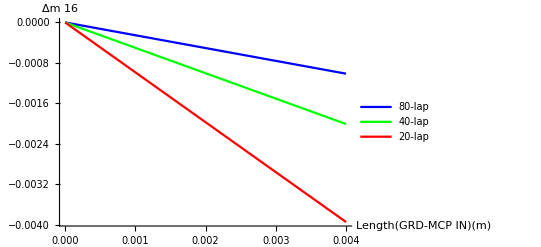

```mathematica
Show[ 
Plot[t2m[ TOF[m,n,Va,V,L],Va,fLength[n]]-m/.{m->16,n->80,V->5000},{L,0,0.004}, PlotRange->{All,{All,0.001}},PlotStyle->Blue, AxesLabel->{"Length(GRD-MCP IN)(m)","Δm 16"},PlotLegends->{"80-lap"}]
,Plot[t2m[ TOF[m,n,Va,V,L],Va,fLength[n]]-m/.{m->16,n->40,V->5000},{L,0,0.004},PlotStyle->Green, AxesLabel->{"L(GRD-MCP IN)(m)","Δm 16"},PlotLegends->{"40-lap"}]
,Plot[t2m[ TOF[m,n,Va,V,L],Va,fLength[n]]-m/.{m->16,n->20,V->5000},{L,0,0.004},PlotStyle->Red, AxesLabel->{"L(GRD-MCP IN)(m)","Δm 16"},PlotLegends->{"20-lap"}]
]
```

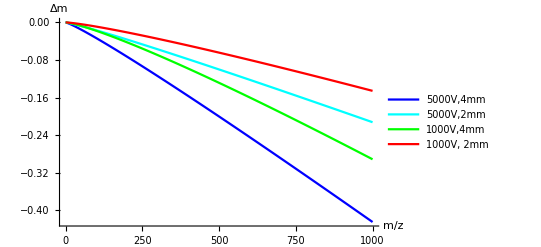

```mathematica
Show[ 
Plot[t2m[ TOF[m,n,Va,V,L],Va,fLength[n]]-m/.{n->20,V->5000,L->0.004},{m,0,1000}, PlotRange->{All,All},PlotStyle->Blue, AxesLabel->{"m/z","Δm"},PlotLegends->{"5000V,4mm"}]
,Plot[t2m[ TOF[m,n,Va,V,L],Va,fLength[n]]-m/.{n->20,V->5000,L->0.002},{m,0,1000}, PlotRange->{All,All},PlotStyle->Cyan, AxesLabel->{"m/z","Δm"},PlotLegends->{"5000V,2mm"}]
,Plot[t2m[ TOF[m,n,Va,V,L],Va,fLength[n]]-m/.{n->20,V->1000,L->0.004},{m,0,1000}, PlotRange->{All,All},PlotStyle->Green, AxesLabel->{"m/z","Δm"},PlotLegends->{"1000V,4mm"}]
,Plot[t2m[ TOF[m,n,Va,V,L],Va,fLength[n]]-m/.{n->20,V->1000,L->0.002},{m,0,1000}, PlotRange->{All,All},PlotStyle->Red, AxesLabel->{"m/z","Δm"},PlotLegends->{"1000V, 2mm"}]
]
```

# Virtual scan-law simulation (MCP IN 5kV)

```mathematica
{tof,nlap,mass} =  {MTOF[[All,2,1]],MTOF[[All,2,2]],MTOF[[All,1]] };
oError = Transpose[{mass,1000 *(t2m[tof-t0,Va,fLength[nlap]]-mass)}];
```

```mathematica
xdata[vmass_,vtof_]:=Transpose[{Sqrt[vmass]*fLength[vtof[[All,2]]], vtof[[All,1]]}];
xerrors[mass_,tof_,Vp_,t0_]:=Transpose[{mass,10^3 (t2m[tof[[All,1]]-t0,Vp,fLength[ tof[[All,2]]]]-mass)}];
xLegends = { "30-lap","40-lap","50-lap"};
xColors = {Red,Blue,Green}
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]}

```mathematica
vMass = { 16.,28.,44.,132. };
 (*TOF[m_,n_,Vp_,Vd_,L_]*)
vt0 = 0.24 10^-6;
v5Tof = { Transpose[{TOF[ vMass,n,Va,Vd,L]+vt0,ConstantArray[n,Length[vMass]]}/.n->30]
       ,Transpose[{TOF[ vMass,n,Va,Vd,L]+vt0,ConstantArray[n,Length[vMass]]}/.n->40]
        ,Transpose[{TOF[vMass,n,Va,Vd,L]+vt0,ConstantArray[n,Length[vMass]]}/.n->50] }/.{Vd->5000,L->0.004};
x5Data = xdata[Join[vMass,vMass,vMass],Join @@v5Tof];
```

FittedModel[2.40578×10^-7+1.14772×10^-6 x]

{2.40578×10^-7,3934.04}

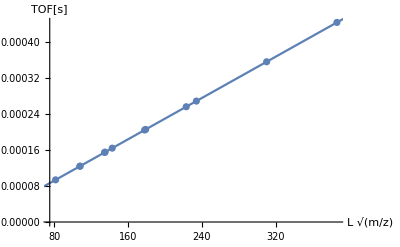

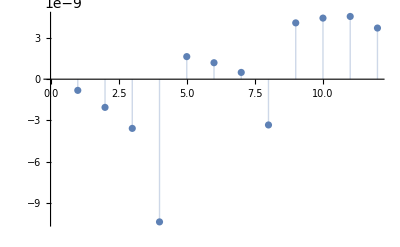

```mathematica
x5m = LinearModelFit[x5Data,x,x]
{x5t0,x5Vacc} = {x5m[0],acceleratorVoltage[x5m[1]-x5m[0],1,1] }(* mass = 1, length = 1m*)
Show[ListPlot[x5Data,AxesLabel->{L Sqrt[m/z],"TOF[s]"}],Plot[x5m[x],{x,0,500},PlotRange->{{0,All},All}]]
ListPlot[x5m["FitResiduals"], Filling -> Axis]
```

```mathematica
x5Errors = xerrors @@ {vMass,#,x5Vacc,x5t0}&/@v5Tof
```

{{{16.,-0.27812},{28.,-0.927567},{44.,-2.02932},{132.,-10.1959}},{{16.,0.423477},{28.,0.408464},{44.,0.21052},{132.,-2.46783}},{{16.,0.848471},{28.,1.21777},{44.,1.56731},{132.,2.21349}}}

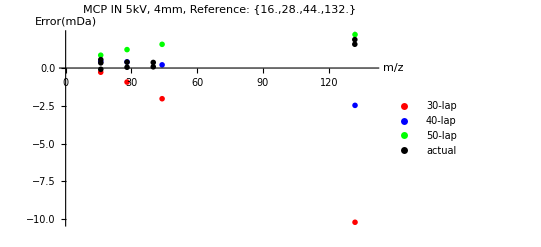

```mathematica
Show[ 
ListPlot[ x5Errors,PlotStyle->xColors,PlotMarkers->"OpenMarkers" ,PlotLegends->xLegends,PlotRange->{{0,140}, {All,All}}]
,ListPlot[ oError,PlotStyle->Black,PlotMarkers->X,PlotLegends->{"actual"}]
,AxesLabel->{m/z,"Error(mDa)"}
,PlotLabel->StringForm["MCP IN 5kV, 4mm, Reference: ``", vMass]
]
```

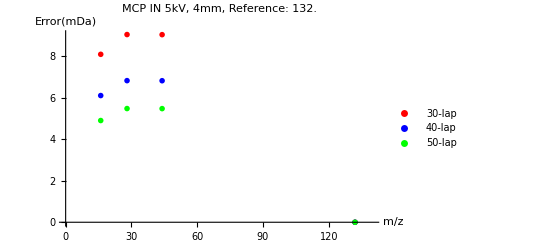

```mathematica
calRefs = {{ 132. },{28.}};
calMass = calRefs[[1]];
dt0 = vt0;
calTof = { Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->30]
       ,Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->40]
        ,Transpose[{TOF[calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->50] }/.{Vd->5000,L->0.004};
calData = xdata[Join[calMass,calMass,calMass],Join @@calTof];
calModel= LinearModelFit[calData,x,x];
{calt0,calVacc} = {calModel[0],acceleratorVoltage[calModel[1]-calModel[0],1,1] }(* mass = 1, length = 1m*);
xErrors = xerrors @@ {vMass,#,calVacc,calt0}&/@v5Tof;
Show[ 
ListPlot[ xErrors,PlotStyle->xColors,PlotMarkers->"OpenMarkers" ,PlotLegends->xLegends,PlotRange->{{0,140}, {All,All}}]
,AxesLabel->{m/z,"Error(mDa)"}
,PlotLabel->"MCP IN 5kV, 4mm, Reference: 132."
]
```

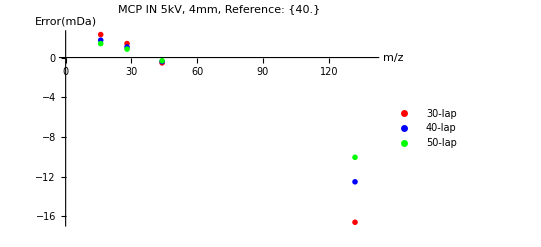

```mathematica
calMass = {40.};
calTof = { Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->30]
       ,Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->40]
        ,Transpose[{TOF[calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->50] }/.{Vd->5000,L->0.004};
calData = xdata[Join[calMass,calMass,calMass],Join @@calTof];
calModel= LinearModelFit[calData,x,x];
{calt0,calVacc} = {calModel[0],acceleratorVoltage[calModel[1]-calModel[0],1,1] }(* mass = 1, length = 1m*);
xErrors = xerrors @@ {vMass,#,calVacc,calt0}&/@v5Tof;
Show[ 
ListPlot[ xErrors,PlotStyle->xColors,PlotMarkers->"OpenMarkers" ,PlotLegends->xLegends,PlotRange->{{0,140}, {All,All}}]
,AxesLabel->{m/z,"Error(mDa)"}
,PlotLabel->StringForm["MCP IN 5kV, 4mm, Reference: ``", calMass]
]
```

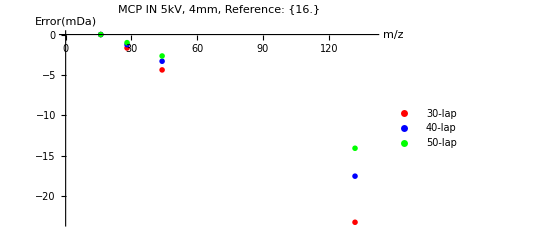

```mathematica
calMass = {16.};
calTof = { Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->30]
       ,Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->40]
        ,Transpose[{TOF[calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->50] }/.{Vd->5000,L->0.004};
calData = xdata[Join[calMass,calMass,calMass],Join @@calTof];
calModel= LinearModelFit[calData,x,x];
{calt0,calVacc} = {calModel[0],acceleratorVoltage[calModel[1]-calModel[0],1,1] }(* mass = 1, length = 1m*);
xErrors = xerrors @@ {vMass,#,calVacc,calt0}&/@v5Tof;
Show[ 
ListPlot[ xErrors,PlotStyle->xColors,PlotMarkers->"OpenMarkers" ,PlotLegends->xLegends,PlotRange->{{0,140}, {All,All}}]
,AxesLabel->{m/z,"Error(mDa)"}
,PlotLabel->StringForm["MCP IN 5kV, 4mm, Reference: ``", calMass]
]
```

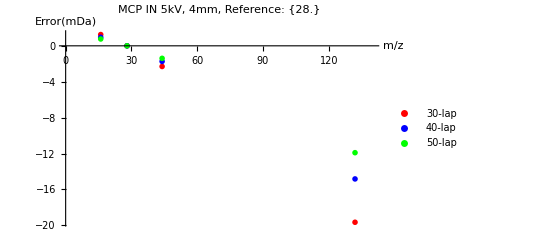

```mathematica
calMass = {28.};
calTof = { Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->30]
       ,Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->40]
        ,Transpose[{TOF[calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->50] }/.{Vd->5000,L->0.004};
calData = xdata[Join[calMass,calMass,calMass],Join @@calTof];
calModel= LinearModelFit[calData,x,x];
{calt0,calVacc} = {calModel[0],acceleratorVoltage[calModel[1]-calModel[0],1,1] }(* mass = 1, length = 1m*);
xErrors = xerrors @@ {vMass,#,calVacc,calt0}&/@v5Tof;
Show[ 
ListPlot[ xErrors,PlotStyle->xColors,PlotMarkers->"OpenMarkers" ,PlotLegends->xLegends,PlotRange->{{0,140}, {All,All}}]
,AxesLabel->{m/z,"Error(mDa)"}
,PlotLabel->StringForm["MCP IN 5kV, 4mm, Reference: ``", calMass]
]
```

### Virtual Scan law simulation (MCP IN 1kV)

{{81.458,0.0000937351},{107.759,0.000123922},{135.083,0.000155282},{233.97,0.000268776},{107.967,0.000124163},{142.827,0.000164173},{179.043,0.00020574},{310.112,0.000356173},{134.476,0.00015459},{177.896,0.000204425},{223.004,0.000256199},{386.254,0.000443569}}

{2.42076×10^-7,3933.78}

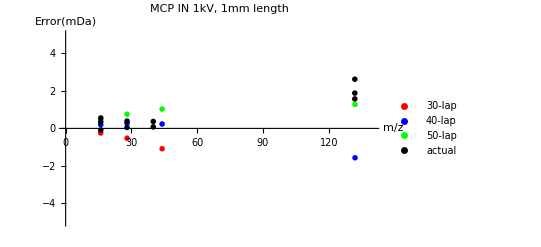

```mathematica
v1Tof = { Transpose[{TOF[ vMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[vMass]]}/.n->30]
       ,Transpose[{TOF[ vMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[vMass]]}/.n->40]
        ,Transpose[{TOF[vMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[vMass]]}/.n->50] }/.{Vd->1000,L->0.004};
x1Data = xdata[Join[vMass,vMass,vMass],Join @@v1Tof]
x1m = LinearModelFit[x1Data,x,x];
{x1t0,x1Vacc} = {x1m[0],acceleratorVoltage[x1m[1]-x1m[0],1,1] }(* mass = 1, length = 1m*)
(*ListPlot[xm["FitResiduals"], Filling -> Axis]*)
x1Errors = xerrors @@ {vMass,#,x1Vacc,x1t0}&/@v1Tof;
Show[ 
ListPlot[ x1Errors,PlotStyle->xColors,PlotMarkers->"OpenMarkers" ,PlotLegends->xLegends,PlotRange->{{0,140}, {-5,5}}]
,ListPlot[ oError,PlotStyle->Black,PlotMarkers->X,PlotLegends->{"actual"}]
,AxesLabel->{m/z,"Error(mDa)"}
,PlotLabel->"MCP IN 1kV, 1mm length"
]
```

{2.36812×10^-7,3933.4}

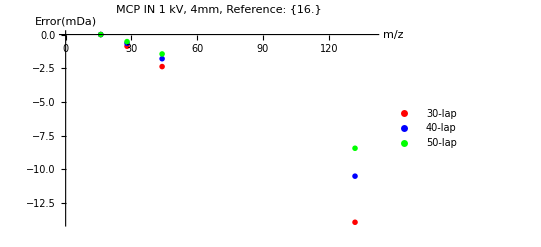

```mathematica
calMass = {16.};
calTof = { Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->30]
       ,Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->40]
        ,Transpose[{TOF[calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->50] }/.{Vd->1000,L->0.004};
calData = xdata[Join[calMass,calMass,calMass],Join @@calTof];
calModel= LinearModelFit[calData,x,x];
{calt0,calVacc} = {calModel[0],acceleratorVoltage[calModel[1]-calModel[0],1,1] }(* mass = 1, length = 1m*)
xErrors = xerrors @@ {vMass,#,calVacc,calt0}&/@v1Tof;
Show[ 
ListPlot[ xErrors,PlotStyle->xColors,PlotMarkers->"OpenMarkers" ,PlotLegends->xLegends,PlotRange->{{0,140}, {All,All}}]
,AxesLabel->{m/z,"Error(mDa)"}
,PlotLabel->StringForm["MCP IN 1 kV, 4mm, Reference: ``", calMass]
]
```

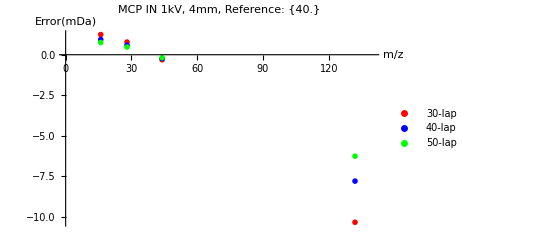

```mathematica
calMass = {40.};
calTof = { Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->30]
       ,Transpose[{TOF[ calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->40]
        ,Transpose[{TOF[calMass,n,Va,Vd,L]+dt0,ConstantArray[n,Length[calMass]]}/.n->50] }/.{Vd->1000,L->0.004};
calData = xdata[Join[calMass,calMass,calMass],Join @@calTof];
calModel= LinearModelFit[calData,x,x];
{calt0,calVacc} = {calModel[0],acceleratorVoltage[calModel[1]-calModel[0],1,1] }(* mass = 1, length = 1m*);
xErrors = xerrors @@ {vMass,#,calVacc,calt0}&/@v1Tof;
Show[ 
ListPlot[ xErrors,PlotStyle->xColors,PlotMarkers->"OpenMarkers" ,PlotLegends->xLegends,PlotRange->{{0,140}, {All,All}}]
,AxesLabel->{m/z,"Error(mDa)"}
,PlotLabel->StringForm["MCP IN 1kV, 4mm, Reference: ``", calMass]
]
```